```mathematica
Cc=0.001
R = 1974
α= 1/(Cc  R)
Solve[1/20==Exp[-α*t],t]
```

0.001

1974

0.506586

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→5.91358}}

NDSolve::deqn: Equation or list of equations expected instead of 0 in the first argument {-0.000506586 ⅇ^(-0.506586 t)+0.506586 (0.256629+0.001 ⅇ^Times[«2»]+100. (Times[«2»]+Times[«2»]))+100. (0.0506586 Cos[Times[«2»]]+0.01 Sin[Times[«2»]])==Sin[0.1 t],0}.

NDSolve::deqn: Equation or list of equations expected instead of 0 in the first argument {-0.000506586 ⅇ^(-0.506586 t)+0.506586 (0.256629+0.001 ⅇ^Times[«2»]+25. (Times[«2»]+Times[«2»]))+25. (0.101317 Cos[Times[«2»]]+0.04 Sin[Times[«2»]])==Sin[0.2 t],0}.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolve::deqn: Equation or list of equations expected instead of 0 in the first argument {-0.000506586 ⅇ^(-0.506586 t)+0.506586 (0.256629+0.001 ⅇ^Times[«2»]+11.1111 (Times[«2»]+Times[«2»]))+11.1111 (0.151976 Cos[Times[«2»]]+0.09 Sin[Times[«2»]])==Sin[0.3 t],0}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

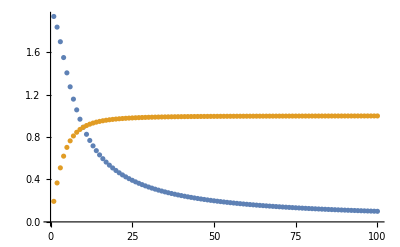

```mathematica
ω=1;
s={};sd={};
Do[
ω=0.1i;
T=2 π/ω;
tmax=10T;
eq = q'[t]+α q[t]==Sin[ω t];
wp=q[0]=0;
sol = NDSolve[{eq,wp},q,{t,0,Tmax}];
f[t_]:=(-ω Cos[t ω]+ α Sin[t ω])/(α^2 + ω^2);
f'[t];
tt1=FindMaxValue[f[t],t];
tt2=FindMaxValue[f'[t],t];
AppendTo[s,tt1];
AppendTo[sd,tt2];
,{i,1,100}];
ListPlot[{s,sd}]
```

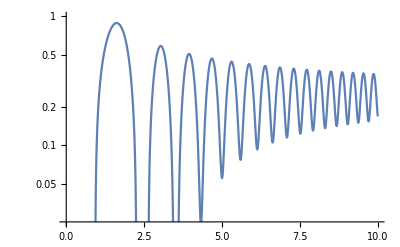

```mathematica
LogPlot[q[ω],{ω,0,10}]
```